```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
NotebookDirectory[]
Off[Needs::nocont];Needs["LowDiscrep`"]; Needs["plots`"]; On[Needs::nocont];
SetOptions[#, Frame->True, Axes->False, FrameStyle->Thick, ImageSize->8*72, LabelStyle->{FontSize->25}] & /@ {Plot, ListPlot, ListLogLogPlot};
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma/

## Sec 2

### 1D low discrepancy vs regular comparisons

```mathematica
npts = 50;
```

```mathematica
region1d={Gray, Opacity[0.5],Polygon[{{0.0,0.0},{0.2,0}, {1.0, 0.8}, {1.0,1.0}, {0.8, 1.0}, {0.0,0.2}}]};
```

```mathematica
rr1 = ListPlot[generateRandomGrid[npts], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
rr2 = ListPlot[RandomReal[{0,1},{npts^2,2}], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
rr3 = ListPlot[generateLDSGrid[npts^2], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
gg= {#1, #1+#2*0.4-0.2} &@@@generateLDSGrid[npts^2];
rr4 = ListPlot[gg, AspectRatio->1, PlotRange->{{0.0,1.0},{-0.2,1.2}},Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
Export["../tex/plots/grid1d-1.pdf", rr1];
Export["../tex/plots/grid1d-2.pdf", rr2];
Export["../tex/plots/grid1d-3.pdf", rr3];
Export["../tex/plots/grid1d-4.pdf", rr4];
```

```mathematica
Clear[gg, rr1, rr2, rr3, rr4, region1d]
```

### 1D interval comparison tests

### Angular cap convergence tests

### 3D Box comparison tests

## Sec 3

### Deep2 mask

```mathematica
(* Make a map of the DEEP2 mask *)
```

```mathematica
deep2 = Import["../data/deep2/windowf.31.fits","RawData"];
deep2meta = Import["../data/deep2/windowf.31.fits","Metadata"];
deep2 = Flatten[deep2, {{1,2},{3}}];
limits = ({{"RALIM0", "DECLIM0"}, {"RALIM1", "DECLIM1"}}/. deep2meta)[[All,All,1]];
ndim = ({"NRA","NDEC"}/.deep2meta)[[All,1]];
dlim = (limits[[2]] - limits[[1]])/ndim;
```

```mathematica
ndim
plotlim = Transpose[limits]- {{351.5,351.5}, {0,0}}
size = Transpose[plotlim][[2]] - Transpose[plotlim][[1]]
```

{1500,1000}

{{-0.129791,0.583069},{-0.103432,0.37705}}

{0.71286,0.480482}

```mathematica
p1 = ArrayPlot[deep2, Frame->False, PlotRangePadding->None, DataReversed->True];
```

```mathematica
p2 = Plot[None, {x, limits[[1,1]], limits[[2,1]]}, PlotRange->plotlim, FrameTicks->{Automatic, Automatic, Automatic, Automatic}, PlotRangePadding->0.005, FrameLabel->{"RA-351.5","Dec"}, AspectRatio->2/3, Epilog->Inset[p1, Transpose[plotlim][[1]],{0,0}, size]];
```

```mathematica
Export["../tex/plots/deep2mask.pdf", p2];
```

### DEEP2 fits

```mathematica
(* Read in all the data files *)
nptlist = {1000, 4000, 16000, 64000, 256000, 1024000, 4096000, 16384000};
bin0 = processbin["../data/deep2/rrdump", 0, nptlist];
bin4 = processbin["../data/deep2/rrdump",4, nptlist];
bin0prng = processbin["../data/deep2_prng/rrdump",0,nptlist];
bin4prng = processbin["../data/deep2_prng/rrdump", 4, nptlist];
jplist = Table[1000*2^i, {i, 0, 8}];
binsjp = readalljp["../data/deep2/counts/",#]& /@ jplist;
```

```mathematica
err[bin_] := Transpose[{bin[[All,1,2]], bin[[All, 2,3]]}];
```

```mathematica
ticklabel = npLogTicks[-6,8];
ticknolabel = npLogTicks[-6,8, ""&];
pticks = {{ticklabel, ticknolabel},{ticklabel,ticknolabel}};
pdata = err /@ {bin0, bin4, bin0prng, bin4prng};
prange = {{700, 3*^7},{3 10^-5,5*10^-2}};
pmarkers = {{npDisk,0.04}, {npSquare,0.04},{npDisk, 0.04}, {npSquare, 0.04}};
pstyle = {{"MediumBlue"},{"Firebrick"}, {FaceForm[],EdgeForm[{Thick,"MediumBlue"}]},{FaceForm[],EdgeForm[{Thick,"Firebrick"}]}}/.ColorData["Legacy", "ColorRules"];
p1 = ListLogLogPlot[pdata, PlotRange->prange,PlotStyle->pstyle,PlotMarkers->pmarkers, FrameTicks->pticks, FrameLabel->{"N_pairs","Relative Error"} ];
p2 = LogLogPlot[20 n^-1, {n, 100, 10^8}, PlotStyle->{AbsoluteDashing[5], Thick, Gray}];
p3 = LogLogPlot[0.7 n^-0.5, {n, 100, 10^8}, PlotStyle->{AbsoluteDashing[10], Thick, Gray}];
Export["../tex/plots/deep2rrcomp1.pdf",Show[p1,p2, p3]]
(*Show[p1,p2,p3]*)
```

../tex/plots/deep2rrcomp1.pdf

```mathematica
(* Now do the comparison with the old-fashioned RR case *)
```

## Scratch

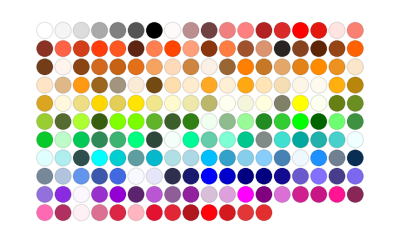

```mathematica
ColorData["Legacy","Panel"]
```

```mathematica
flist= FileNames["../data/deep2/counts/"<>IntegerString[4000]<>"*.dat"]
```

```mathematica
{"../data/deep2/counts/4000_0.dat","../data/deep2/counts/4000_10.dat","../data/deep2/counts/4000_11.dat","../data/deep2/counts/4000_12.dat","../data/deep2/counts/4000_13.dat","../data/deep2/counts/4000_14.dat","../data/deep2/counts/4000_15.dat","../data/deep2/counts/4000_16.dat","../data/deep2/counts/4000_17.dat","../data/deep2/counts/4000_18.dat","../data/deep2/counts/4000_19.dat","../data/deep2/counts/4000_1.dat","../data/deep2/counts/4000_20.dat","../data/deep2/counts/4000_21.dat","../data/deep2/counts/4000_22.dat","../data/deep2/counts/4000_23.dat","../data/deep2/counts/4000_24.dat","../data/deep2/counts/4000_25.dat","../data/deep2/counts/4000_26.dat","../data/deep2/counts/4000_27.dat","../data/deep2/counts/4000_28.dat","../data/deep2/counts/4000_29.dat","../data/deep2/counts/4000_2.dat","../data/deep2/counts/4000_30.dat","../data/deep2/counts/4000_31.dat","../data/deep2/counts/4000_32.dat","../data/deep2/counts/4000_33.dat","../data/deep2/counts/4000_34.dat","../data/deep2/counts/4000_35.dat","../data/deep2/counts/4000_36.dat","../data/deep2/counts/4000_37.dat","../data/deep2/counts/4000_38.dat","../data/deep2/counts/4000_39.dat","../data/deep2/counts/4000_3.dat","../data/deep2/counts/4000_40.dat","../data/deep2/counts/4000_41.dat","../data/deep2/counts/4000_42.dat","../data/deep2/counts/4000_43.dat","../data/deep2/counts/4000_44.dat","../data/deep2/counts/4000_45.dat","../data/deep2/counts/4000_46.dat","../data/deep2/counts/4000_47.dat","../data/deep2/counts/4000_48.dat","../data/deep2/counts/4000_49.dat","../data/deep2/counts/4000_4.dat","../data/deep2/counts/4000_50.dat","../data/deep2/counts/4000_51.dat","../data/deep2/counts/4000_52.dat","../data/deep2/counts/4000_53.dat","../data/deep2/counts/4000_54.dat","../data/deep2/counts/4000_55.dat","../data/deep2/counts/4000_56.dat","../data/deep2/counts/4000_57.dat","../data/deep2/counts/4000_58.dat","../data/deep2/counts/4000_59.dat","../data/deep2/counts/4000_5.dat","../data/deep2/counts/4000_60.dat","../data/deep2/counts/4000_61.dat","../data/deep2/counts/4000_62.dat","../data/deep2/counts/4000_63.dat","../data/deep2/counts/4000_64.dat","../data/deep2/counts/4000_65.dat","../data/deep2/counts/4000_66.dat","../data/deep2/counts/4000_67.dat","../data/deep2/counts/4000_68.dat","../data/deep2/counts/4000_69.dat","../data/deep2/counts/4000_6.dat","../data/deep2/counts/4000_70.dat","../data/deep2/counts/4000_71.dat","../data/deep2/counts/4000_72.dat","../data/deep2/counts/4000_73.dat","../data/deep2/counts/4000_74.dat","../data/deep2/counts/4000_75.dat","../data/deep2/counts/4000_76.dat","../data/deep2/counts/4000_77.dat","../data/deep2/counts/4000_78.dat","../data/deep2/counts/4000_79.dat","../data/deep2/counts/4000_7.dat","../data/deep2/counts/4000_80.dat","../data/deep2/counts/4000_81.dat","../data/deep2/counts/4000_82.dat","../data/deep2/counts/4000_83.dat","../data/deep2/counts/4000_84.dat","../data/deep2/counts/4000_85.dat","../data/deep2/counts/4000_86.dat","../data/deep2/counts/4000_87.dat","../data/deep2/counts/4000_88.dat","../data/deep2/counts/4000_89.dat","../data/deep2/counts/4000_8.dat","../data/deep2/counts/4000_90.dat","../data/deep2/counts/4000_91.dat","../data/deep2/counts/4000_92.dat","../data/deep2/counts/4000_93.dat","../data/deep2/counts/4000_94.dat","../data/deep2/counts/4000_95.dat","../data/deep2/counts/4000_96.dat","../data/deep2/counts/4000_97.dat",,"../data/deep2/counts/4000_99.dat","../data/deep2/counts/4000_9.dat"}
```

```mathematica
Import["../data/deep2/counts/4000_98.dat","Table"]
```

{{1806.98},{Start,Stop,Count},{0.007812,0.015625,5814.17},{0.015625,0.03125,22605.4},{0.03125,0.0625,83130.6},{0.0625,0.125,284241.},{0.125,0.25,853105.}}

```mathematica
readjp["../data/deep2/counts/4000_2.dat"]
```

{0.001797,0.0068941,0.0253154,0.0874932,0.259228}

```mathematica
processbin["../data/deep2/rrdump",0,{16384000}]
```

{{{100,16384000,0.007812,0.015625},{0.00179232,7.44189×10^-8,0.000041521}}}